```mathematica
<<emittanceellipse`
```

```mathematica
SetDirectory["C:\\anaconda32\\work\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\test_4"]
```

C:\anaconda32\work\OnlineModel\SimulationFramework\Examples\CLARA\test_4

```mathematica
Import["CLA-FMS-APER-01.hdf5","/beam/columns"]
```

{x,y,z,cpx,cpy,cpz,t,q}

```mathematica
{x,y,z,cpx,cpy,cpz,t,q}=Transpose[beam=Import["CLA-FMS-APER-01.hdf5","/beam/beam"]];
```

```mathematica
cp=√(cpx^2+cpy^2+cpz^2);
```

```mathematica
volume[{a_,b_}]:=(Max[a]-Min[a])*(Max[b]-Min[b])
```

```mathematica
{volume[{x,cpx/cpz}],volume[{y,cpy/cpz}],volume[{z-Mean[z],(cpz/Mean[cp]-1)}]}
```

{1.99429×10^-6,1.64161×10^-6,1.36226×10^-6}

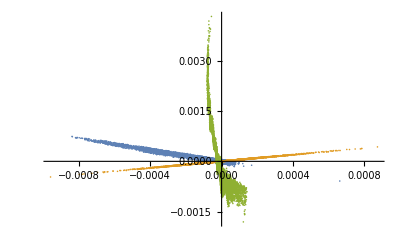

```mathematica
ListPlot[{Transpose[{x,cpx/cpz}],Transpose[{y,cpy/cpz}],Transpose[{z-Mean[z],(cpz/Mean[cp]-1)}]},PlotRange->All]
```

```mathematica
emitans=.;
```

```mathematica
P=(*#-Mean[#]&/@*)Transpose[beam][[{1,2},1;;-1;;3]];
```

```mathematica
emitans=emitansg=emittanceGaussian[P]
```

{{4.20275×10^-8,0.393469},{0.000327113,0.00012848,1.5732,0.,0.},{0.00517265,0.392781,2.54601}}

```mathematica
N[1-Exp[-1^2/2]]
```

0.393469

```mathematica
emitans=emittanceEllipse[emitans,P,10^-6,N[1-Exp[-1^2/2]]]
```

{{5.37388×10^-8,0.393324},{0.000494961,0.000108572,1.60926,-0.000104355,-0.0000497095},{0.166728,0.225769,4.55243}}

```mathematica
covellipse=Block[{a,b,c, x0, px0},
{a,b,c, x0, px0}=#[[2]];
Graphics[{Opacity[0.3],Red,Translate[Rotate[Scale[Disk[{0, 0}, Abs[{a,b}]],1], c], { x0, px0}]},Frame->True]
]&[emitansg];
Show[emittanceEllipsePlot[P,emitans],covellipse,Frame->True,ImageSize->Large]
```

-Graphics-

```mathematica
Clear[emitans90];
```

```mathematica
emitans90=emittanceEllipse[emitans90,P,10^-30,0.9]
```

{{1.58×10^-7,0.899943},{0.000249285,0.000633814,0.00942465,-0.0000942719,-1.5617×10^-6},{0.0202544,0.393501,2.54233}}

```mathematica
covellipse=Block[{a,b,c,x0,px0},
{a,b,c,x0,px0}=#[[2]];
Graphics[{Opacity[0.3],Red,Translate[Rotate[Scale[Disk[{0, 0}, Abs[{a,b}]],1], c], {x0,px0}]},Frame->True]
]&[emitansg];
Show[emittanceEllipsePlot[P,emitans90],covellipse,Frame->True,ImageSize->Large]
```

-Graphics-

```mathematica
Clear[emitans99];
```

```mathematica
emitans99=emittanceEllipse[emitans99,P,10^-12,0.99]
```

{{2.49434×10^-7,0.989548},{0.000358515,0.000695743,0.0378183,-0.000141199,0.0000127432},{0.0538522,0.517335,1.93859}}

```mathematica
covellipse=Block[{a,b,c,x0,px0},
{a,b,c,x0,px0}=#[[2]];
Graphics[{Opacity[0.3],Red,Translate[Rotate[Scale[Disk[{0, 0}, Abs[{a,b}]],1], c], {x0,px0}]},Frame->True]
]&[emitansg];
Show[emittanceEllipsePlot[P,emitans99],covellipse,Frame->True,ImageSize->Large]
```

-Graphics-